Data Import

```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210224_impacts_in_time_windows"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
data=Import["../data/ccm_manipulated_396096_partitioned_in_time_windows.mx",HeaderLines->1];
```

```mathematica
Print["Weight Zero Rows: ",Length@Position[data[[10]][[All,11]],0]]
Print["Thickness + Width + Length Zero Rows: ",Length@Position[data[[10]][[All,9]],0]]
Print["Usable Rows: ",Length@data[[10]]-Length@Position[data[[10]][[All,9]],0]]
```

Weight Zero Rows: 0

Thickness + Width + Length Zero Rows: 0

Usable Rows: 396096

Investigation of Constraints Impact in Time Windows

Fixed Step Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[9,15,10];]
```

{230.982,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedstep[[1]][[i]],widthdataintimewindowsFixedstep[[2]][[i]],2,7,400,Green],{i,Range@10}];
```

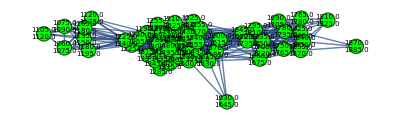
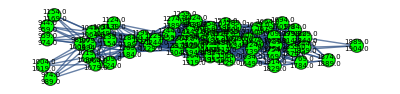
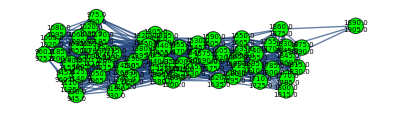
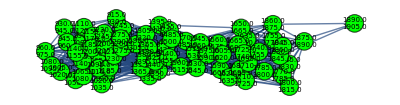
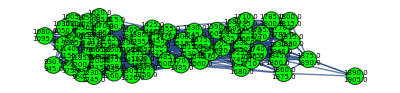
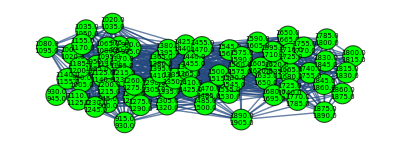
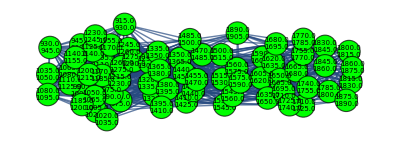
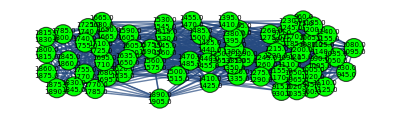
{{-Graphics-,52},{-Graphics-,63},{-Graphics-,66},{-Graphics-,66},{-Graphics-,66},{-Graphics-,66},{-Graphics-,66},{-Graphics-,66},{-Graphics-,66},{-Graphics-,67}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
GirwanNewmanmodularity[xx_]:=Module[{network,m,Aij,B,u,β,s,Q},
network=xx;
m=EdgeCount@network;
Aij=AdjacencyMatrix@network;
B=N@(Aij-Outer[Times,VertexDegree@network,VertexDegree@network]/(2*m));
u=Eigenvectors@B;
β=Eigenvalues@B;
s=(u/.x_/;x<0->-1)/.x_/;x>0->1;
Q=(Total@(Table[(u[[i]].Flatten@s[[Flatten@Position[β,Max@β]]])^2,{i,VertexList@network}]*β))/(4*m)]
```

```mathematica
GNmodularityvalues=Table[GirwanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
div1=Flatten@Position[Flatten@s[[Flatten@Position[β,Max@β]]],_?Negative];
div2=Flatten@Position[Flatten@s[[Flatten@Position[β,Max@β]]],_?Positive];
Bij=Table[Aij[[i,i]],{i,{div1,div2}}];
(* mg=Total@Table[Total@Bij[[All,i]],{i,Length@Bij}]/2;*)
Bg=Table[N@ReplacePart[Bij[[j]],MapThread[{#1,#1}->#2&,{Range@Length@Bij[[j]],-Table[Total@(Bij[[j]])[[All,i]],{i,Length@Bij[[j]]}]}]],{j,{div1,div2}}];
ug=Table[Eigenvectors@Bg[[i]],{i,{div1,div2}}];
βg=Table[Eigenvalues@Bg[[i]],{i,{div1,div2}}];
sg=Table[(ug[[i]]/.x_/;x<0->-1)/.x_/;x>0->1,{i,{div1,div2}}];
deltaQ=Table[(Total@(Table[((ug[[j]])[[i]].Flatten@(sg[[j]])[[Flatten@Position[βg[[j]],Max@βg[[j]]]]])^2,{i,Length@Bij[[j]]}]*βg[[j]]))/(4*m),{j,{div1,div2}}]
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{3,3,3,2,2,2,2,2,2,3}

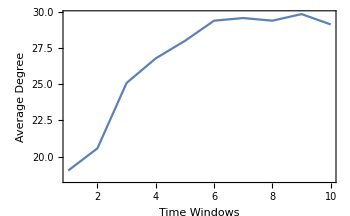
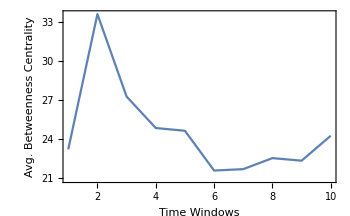
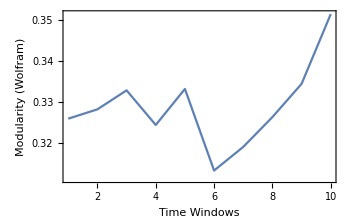
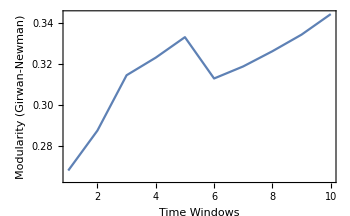

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girwan-Newman)"},ImageSize->350,PlotRange->{{1,10},All}]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[10,0.2,10];]
```

{633.153,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedstep[[1]][[i]],thicknessdataintimewindowsFixedstep[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@10}];
```

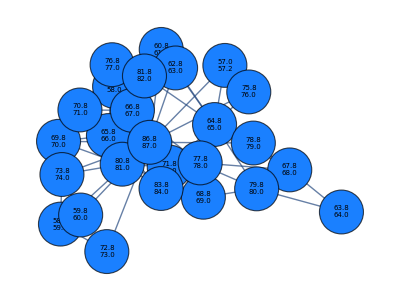
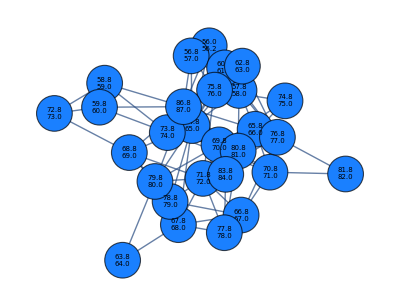
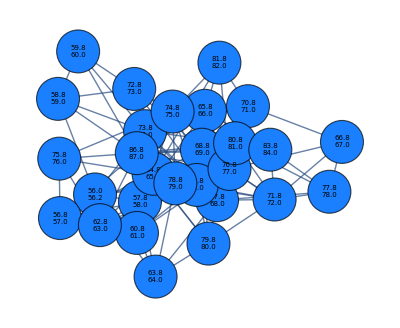
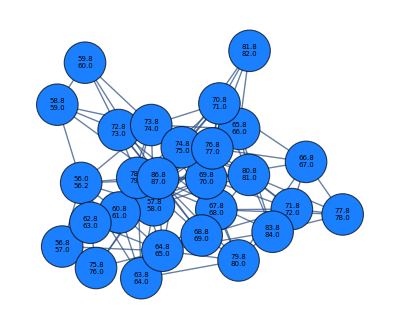
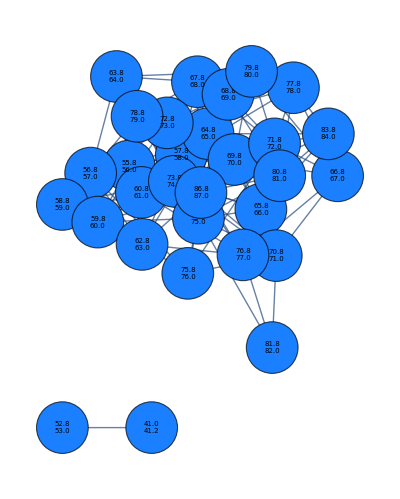
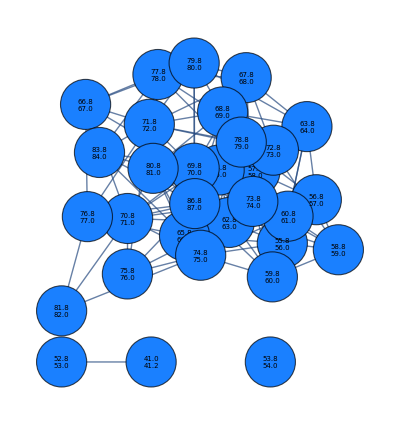
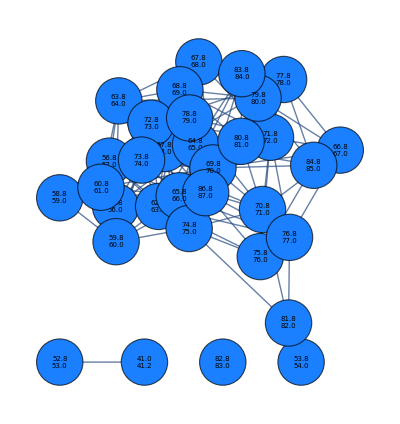
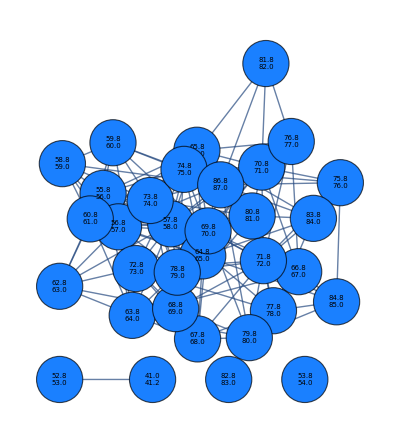
{{-Graphics-,26},{-Graphics-,28},{-Graphics-,28},{-Graphics-,28},{-Graphics-,30},{-Graphics-,31},{-Graphics-,33},{-Graphics-,33},{-Graphics-,35},{-Graphics-,35}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
GNmodularityvalues=Table[GirwanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{4,4,4,4,4,4,6,5,5,4}

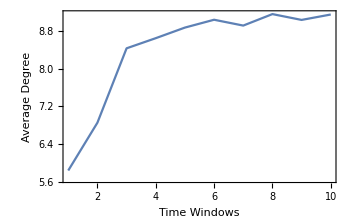
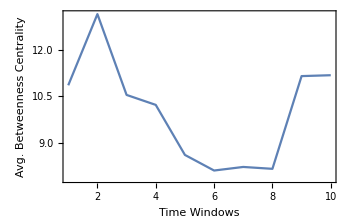
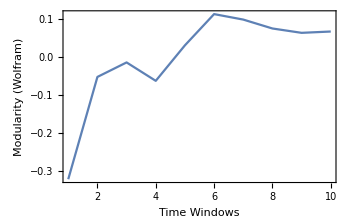
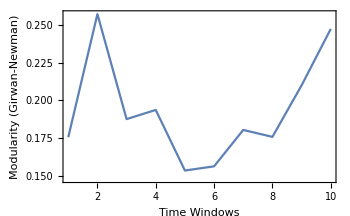

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girwan-Newman)"},ImageSize->350,PlotRange->{{1,10},All}]}
```

Length Feature

```mathematica
AbsoluteTiming[lengthdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[12,600,10];]
```

{229.445,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[lengthdataintimewindowsFixedstep[[1]][[i]],lengthdataintimewindowsFixedstep[[2]][[i]],2,7,400,RGBColor[1.,0.53,0.2]],{i,Range@10}];
```

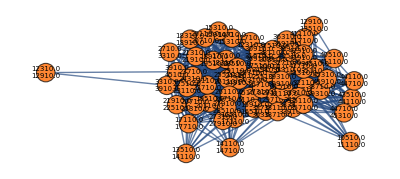
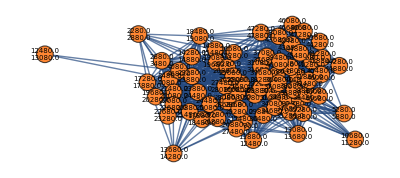
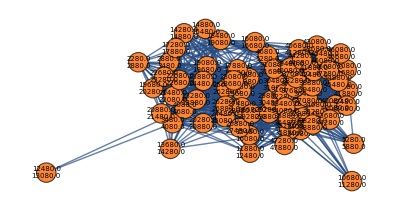
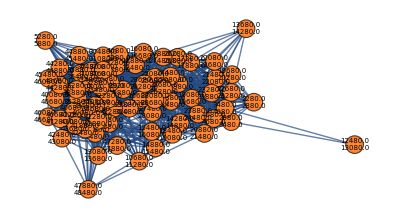
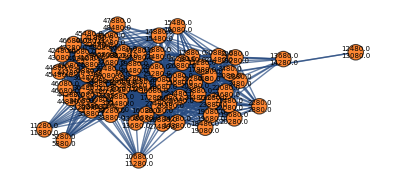
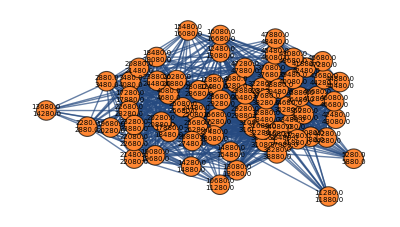
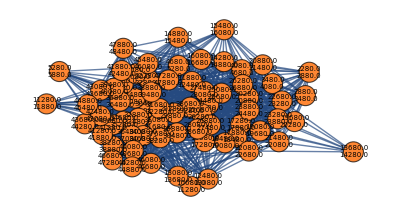
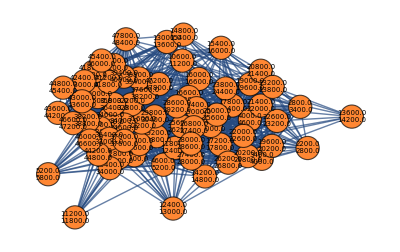
{{-Graphics-,61},{-Graphics-,67},{-Graphics-,67},{-Graphics-,68},{-Graphics-,69},{-Graphics-,69},{-Graphics-,69},{-Graphics-,69},{-Graphics-,70},{-Graphics-,70}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
GNmodularityvalues=Table[GirwanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,2,2,2,2,2,2,2,2,2}

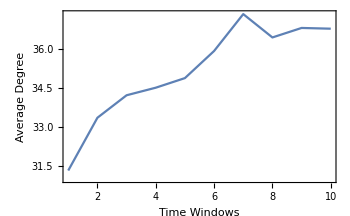
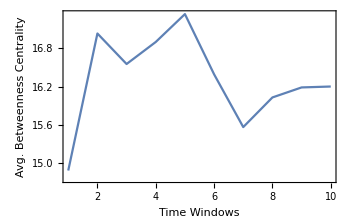
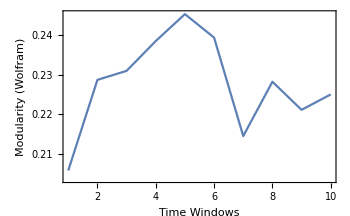
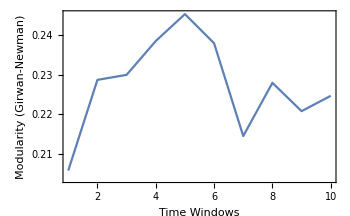

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girwan-Newman)"},ImageSize->350,PlotRange->{{1,10},All}]}
```

Weight Feature

```mathematica
AbsoluteTiming[weightdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[11,600,10];]
```

{164.225,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[weightdataintimewindowsFixedstep[[1]][[i]],weightdataintimewindowsFixedstep[[2]][[i]],2,7,400,Red],{i,Range@10}];
```

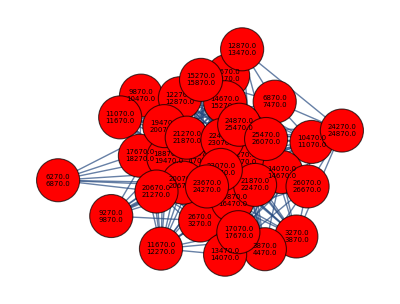
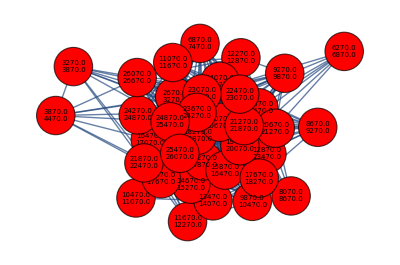
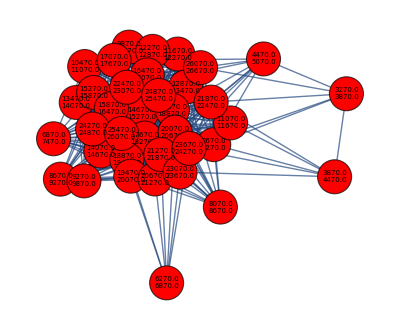
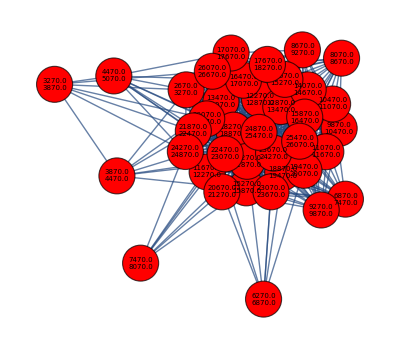
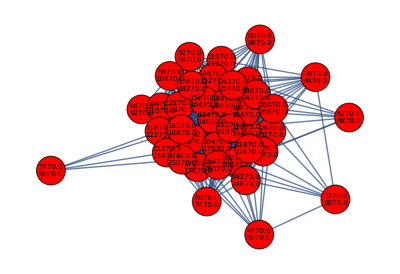
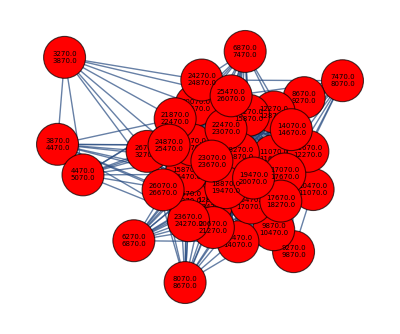
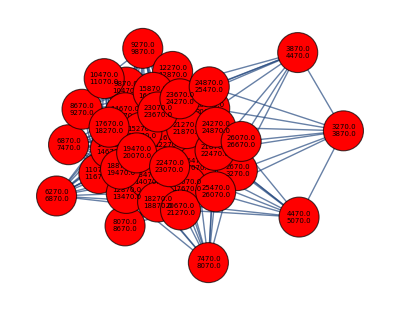
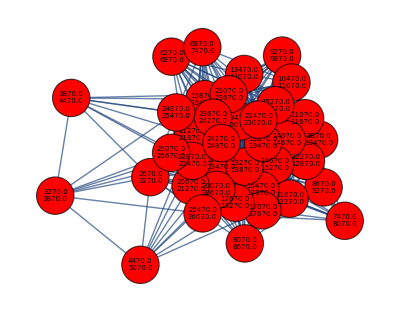
{{-Graphics-,35},{-Graphics-,36},{-Graphics-,37},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
GNmodularityvalues=Table[GirwanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{3,3,3,3,2,2,2,2,2,2}

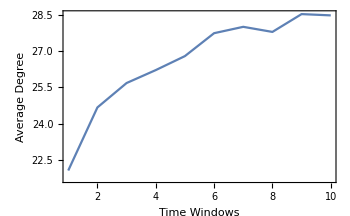
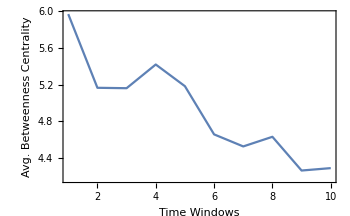
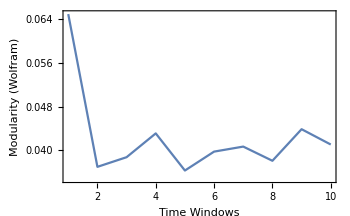
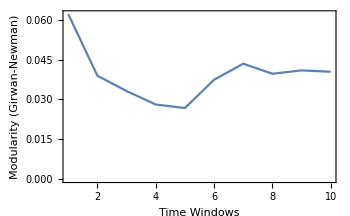

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girwan-Newman)"},ImageSize->350,PlotRange->{{1,10},All}]}
```

Fixed Bucket Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[9,60,10];]
```

{2159.36,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedbucket[[1]][[i]],widthdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,Green],{i,Range@10}];
```

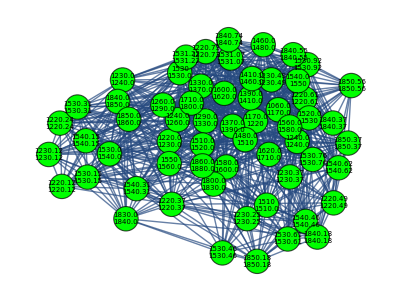
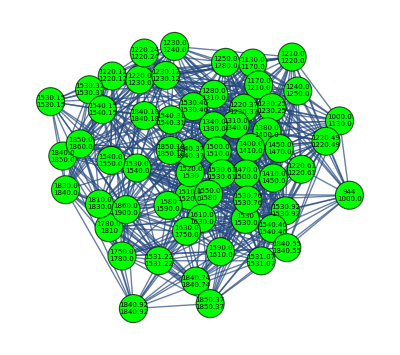
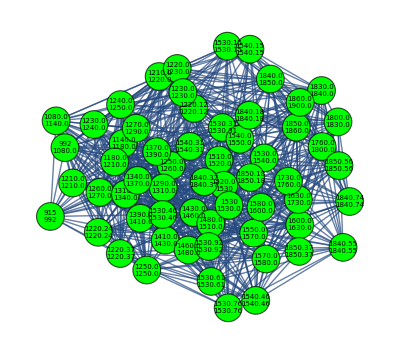
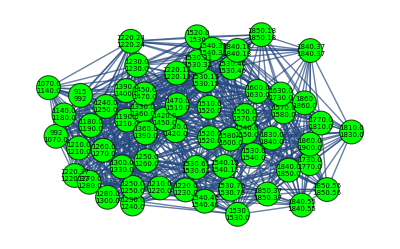
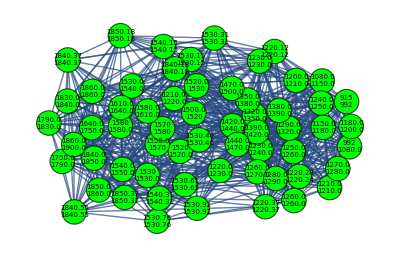
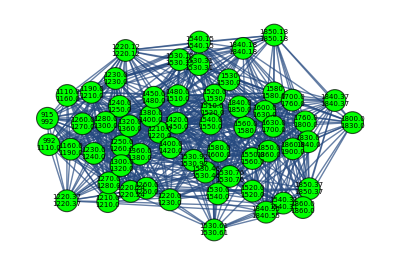
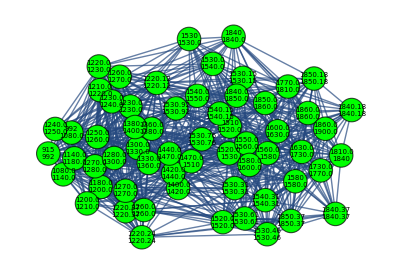
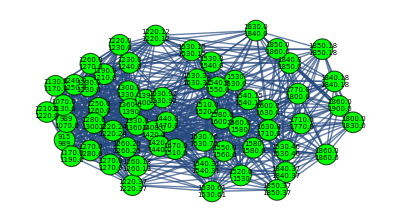
{{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

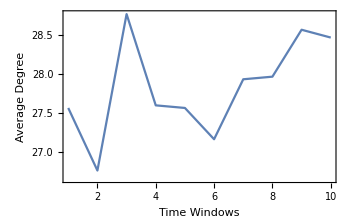
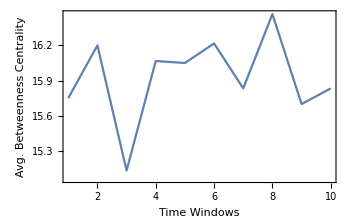
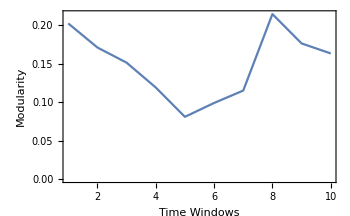

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->{{1,10},All}]}
```

Thickness Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[9,60,10];]
```

{2159.36,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedbucket[[1]][[i]],widthdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,Green],{i,Range@10}];
```

```mathematica
graphsandnodenumbers
```

{{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60}}

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->{{1,10},All}]}
```

{-Graphics-,-Graphics-,-Graphics-}

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdatawithfxdbucketintimewindows=snetworkdatafxdbucketintimewindows[10,55,10];]
```

{3701.96,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdatawithfxdbucketintimewindows[[1]][[i]],thicknessdatawithfxdbucketintimewindows[[2]][[i]],1.5,7,600,RGBColor[0.1,0.5,1.]],{i,Range@10}];
```

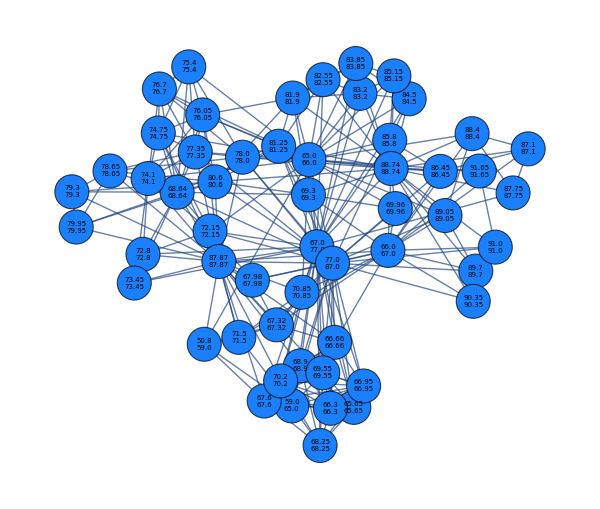
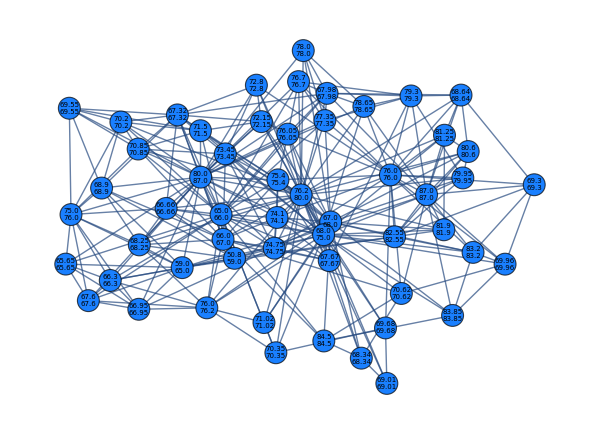
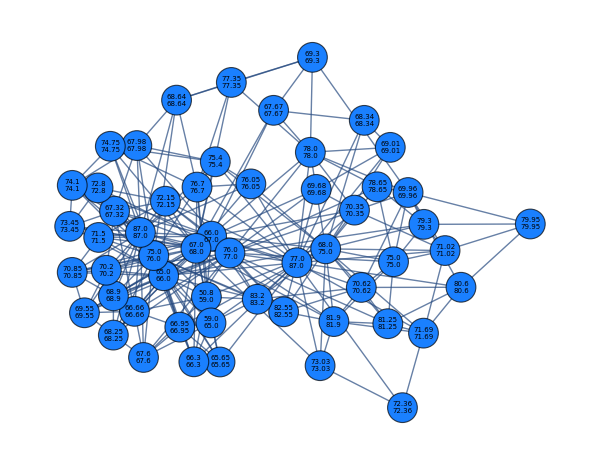
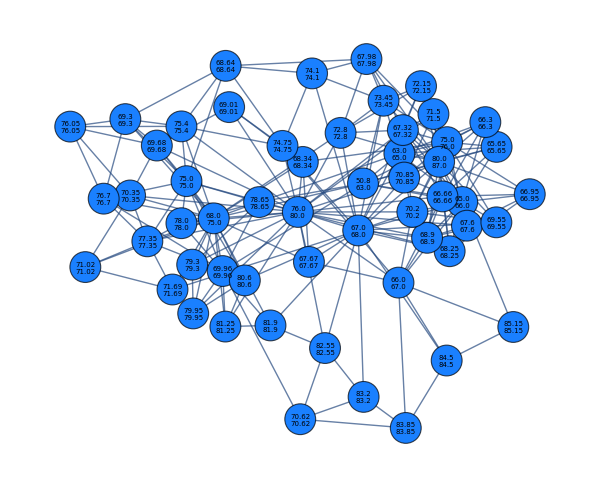
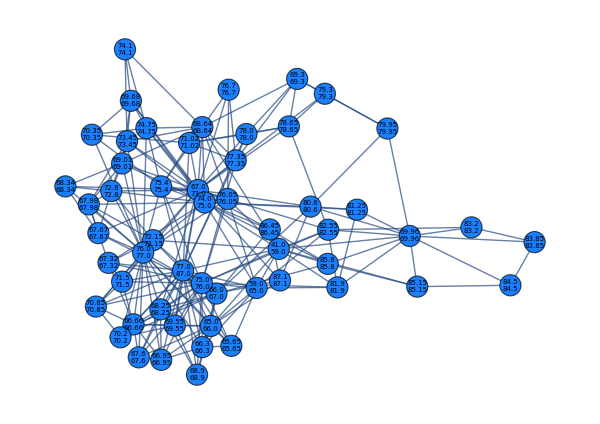
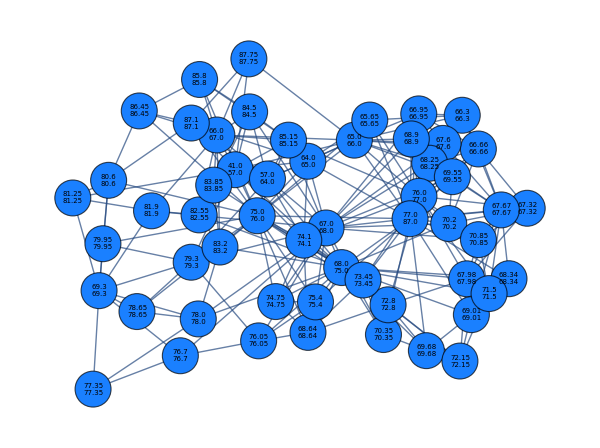
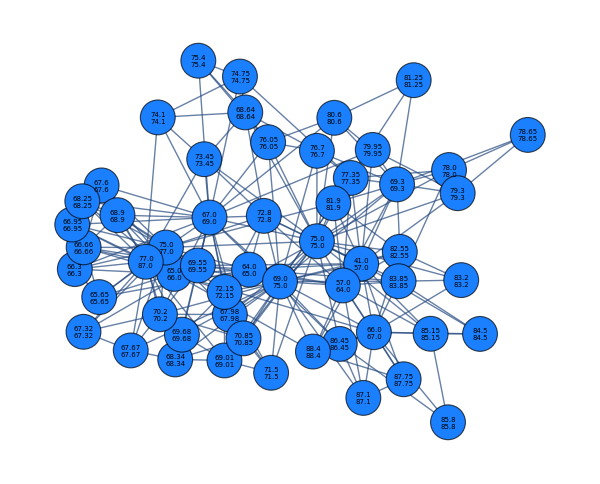
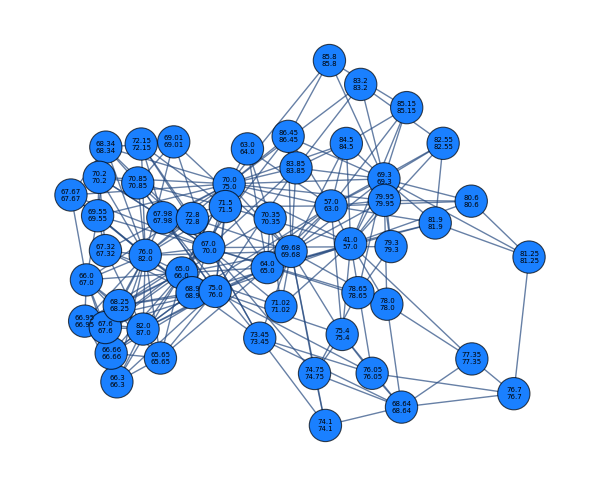
{{-Graphics-,55},{-Graphics-,55},{-Graphics-,55},{-Graphics-,55},{-Graphics-,55},{-Graphics-,55},{-Graphics-,55},{-Graphics-,55},{-Graphics-,55},{-Graphics-,55}}

```mathematica
graphsandnodenumbers
```

```mathematica
correlationvaluesthroughwindowsspearman=Table[correlationfunction[i,1],{i,graphsandnodenumbers[[All,1]]}];
correlationvaluesthroughwindowspearson=Table[correlationfunction[i,2],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
correlationvaluesthroughwindowsspearman
correlationvaluesthroughwindowspearson
```

{{0.767914,-0.845664},{0.829948,-0.829075},{0.629385,-0.868622},{0.729863,-0.79477},{0.727612,-0.853122},{0.678766,-0.873149},{0.778866,-0.877886},{0.678203,-0.862349},{0.863328,-0.853203},{0.726022,-0.85655}}

{{0.925784,-0.731837},{0.951473,-0.682085},{0.879689,-0.681712},{0.831552,-0.596759},{0.864873,-0.721212},{0.885541,-0.626575},{0.931057,-0.705016},{0.910229,-0.712981},{0.938219,-0.621927},{0.917204,-0.651067}}

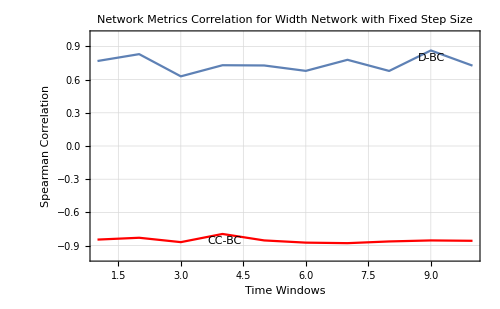
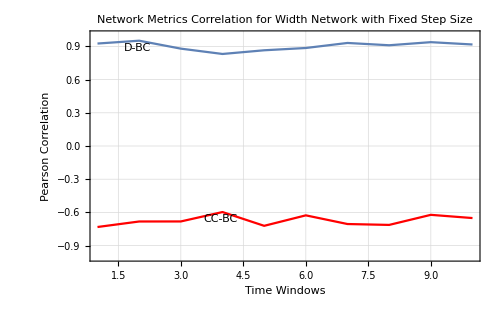

```mathematica
{Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Width Network with Fixed Step Size"],Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Width Network with Fixed Step Size"]}
```

```mathematica
ZscoreDeBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-7.61033},{2,-4.95744},{3,-14.6055},{4,-8.65119},{5,-8.74502},{6,-10.2952},{7,-6.73297},{8,-10.547},{9,-3.03971},{10,-9.2238}}

```mathematica
ZscoreCCBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-4.65096},{2,-4.52137},{3,-4.92712},{4,-4.61019},{5,-5.03007},{6,-4.87373},{7,-4.99681},{8,-5.07192},{9,-4.9179},{10,-4.90242}}

```mathematica
ZscoreDeBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-0.0593356},{2,1.15447},{3,-2.19479},{4,-3.58037},{5,-2.2706},{6,-1.51536},{7,0.267788},{8,-0.603555},{9,0.515586},{10,-0.296038}}

```mathematica
ZscoreCCBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-4.21661},{2,-3.70766},{3,-3.88207},{4,-3.5312},{5,-4.53877},{6,-3.59823},{7,-4.27859},{8,-4.46446},{9,-3.61586},{10,-3.82381}}

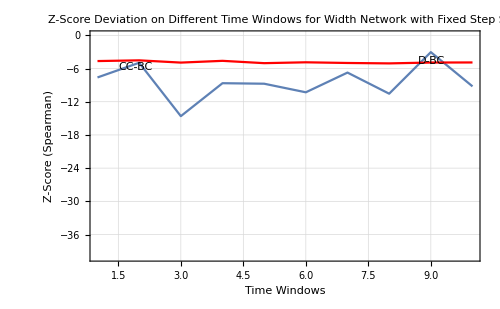
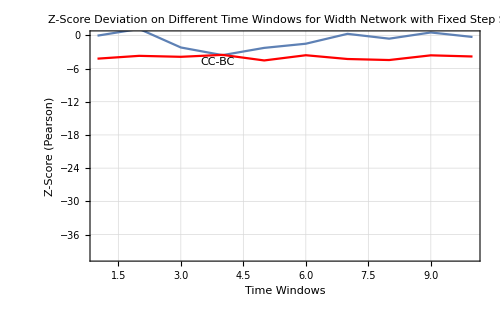

```mathematica
{Show[ListPlot[ZscoreDeBCspearman,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],ListPlot[ZscoreCCBCspearman,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],PlotRange->{All,{-40,0}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Width Network with Fixed Step Size"],Show[ListPlot[ZscoreDeBCpearson,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],ListPlot[ZscoreCCBCpearson,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],PlotRange->{All,{-40,0}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Width Network with Fixed Step Size"]}
```